```mathematica
Table[base->Length[ListofVars[allGraphs5[lambdaKey,Bases[base,"Colofour"]]]],{base,allBases}]
```

{C→11,E→27,G→11,F→26,T→4}

```mathematica
Table[base->allGraphs5[lambdaKey,Bases[base,"Colofour"]]/.RepGraph[base],{base,allBases}]
```

{C→-Graphics-361660+-Graphics-361120+-Graphics-317380+-Graphics-317140+-Graphics-296080+-Graphics-360850+-Graphics-317110+-Graphics-296050+-Graphics-295510+-Graphics-295270+-Graphics-295240,E→4 -Graphics-590481--Graphics-575282--Graphics-544922--Graphics-529762--Graphics-454162--Graphics-408962--Graphics-393922--Graphics-189802--Graphics-63202--Graphics-21242--Graphics-7282+-Graphics-529745+-Graphics-393845+-Graphics-408785+-Graphics-393685+-Graphics-6665+-Graphics-19445+-Graphics-4885+-Graphics-58345+-Graphics-14765+-Graphics-265--Graphics-3936613--Graphics-48613--Graphics-1813--Graphics-145813--Graphics-213+-Graphics-034,G→-Graphics-294400+-Graphics-273340+-Graphics-273100+-Graphics-229360+-Graphics-228820--Graphics-295210--Graphics-294970--Graphics-294430--Graphics-273370--Graphics-229630+-Graphics-295240,F→1/6 (-Graphics-1969213-2 -Graphics-1968615+-Graphics-1968413+-Graphics-664216+-Graphics-658816-2 -Graphics-656215-2 -Graphics-243015+-Graphics-221416+-Graphics-219016+-Graphics-97213-2 -Graphics-81015+-Graphics-73813+-Graphics-24413+-Graphics-8416-2 -Graphics-3615+2 -Graphics-264885--Graphics-219545+2 -Graphics-204485+2 -Graphics-196965--Graphics-87845--Graphics-73745--Graphics-66705+2 -Graphics-31605--Graphics-24605+2 -Graphics-10625+-Graphics-295240),T→--Graphics-390141+-Graphics-258682--Graphics-214203+-Graphics-199365}

```mathematica
Table[base->allGraphs6[lambdaKey,Bases6[base,"Colofour"]]/.RepGraph6[base],{base,allBases6}]
```

{C→-Graphics-12495451+-Graphics-12495505+-Graphics-12136783+-Graphics-12136759+-Graphics-11957506+-Graphics-8834413+-Graphics-8952565+-Graphics-8830039+-Graphics-8946007+-Graphics-8770966+-Graphics-7767133+-Graphics-7765027+-Graphics-7240144+-Graphics-7358188+-Graphics-7708108+-Graphics-12495424+-Graphics-11957449+-Graphics-11957425+-Graphics-12136756+-Graphics-11957503+-Graphics-8775337+-Graphics-8827852+-Graphics-8768779+-Graphics-8946004+-Graphics-8770963+-Graphics-7764946+-Graphics-7240063+-Graphics-7705921+-Graphics-7181041+-Graphics-7358161+-Graphics-7708081+-Graphics-7705975+-Graphics-7181095+-Graphics-7235689+-Graphics-7351603+-Graphics-7176643+-Graphics-7233583+-Graphics-7174537+-Graphics-7351627+-Graphics-7176667+-Graphics-11957422+-Graphics-8768776+-Graphics-7705894+-Graphics-7181014+-Graphics-7233502+-Graphics-7174456+-Graphics-7174480+-Graphics-7351600+-Graphics-7176640+-Graphics-7174534+-Graphics-7174453,E→4 -Graphics-59048--Graphics-54492--Graphics-52976--Graphics-57528--Graphics-45416--Graphics-40896--Graphics-39392--Graphics-18980--Graphics-6320--Graphics-2124--Graphics-728+-Graphics-52974+-Graphics-40878+-Graphics-39368+-Graphics-39384+-Graphics-1944+-Graphics-488+-Graphics-666+-Graphics-5834+-Graphics-1476+-Graphics-26--Graphics-39366--Graphics-486--Graphics-1458--Graphics-2--Graphics-18+-Graphics-0,G→-Graphics-6583879+-Graphics-6581773+-Graphics-5518867+-Graphics-5514493+-Graphics-5402899+-Graphics-5396341+-Graphics-2212147+-Graphics-2212123+-Graphics-1853455+-Graphics-1853401+-Graphics-7108762+-Graphics-6990718+-Graphics-6640798--Graphics-6583960+-Graphics-5577940--Graphics-5521054--Graphics-5402902+-Graphics-2391400--Graphics-2212150--Graphics-1853482-2 -Graphics-7174369-2 -Graphics-7172263-2 -Graphics-7172239-2 -Graphics-7167865-2 -Graphics-7167811--Graphics-7115323--Graphics-7113217--Graphics-7108843--Graphics-6997303--Graphics-6997279--Graphics-6990745--Graphics-6642985--Graphics-6642931--Graphics-6640825--Graphics-5580127--Graphics-5577943--Graphics-5573569--Graphics-2391481--Graphics-2391457--Graphics-2391403+3 -Graphics-7174450+3 -Graphics-7174426+3 -Graphics-7174372+3 -Graphics-7172266+3 -Graphics-7167892+-Graphics-7115404+-Graphics-6997306+-Graphics-6643012+-Graphics-5580130+-Graphics-2391484-4 -Graphics-7174453,F→1/6 (-Graphics-19692-2 -Graphics-19686+-Graphics-19684+-Graphics-6642+-Graphics-6588-2 -Graphics-6562-2 -Graphics-2430+-Graphics-2214+-Graphics-2190+-Graphics-972-2 -Graphics-810+-Graphics-738+-Graphics-244+-Graphics-84-2 -Graphics-36+2 -Graphics-26488--Graphics-21954+2 -Graphics-20448+2 -Graphics-19696--Graphics-8784--Graphics-7374--Graphics-6670+2 -Graphics-3160--Graphics-2460+2 -Graphics-1062+-Graphics-29524)}

```mathematica
Select[Keys[allGraphs4],IsomorphicGraphQ[allGraphs4[#,"graph"],CycleGraph[4]]&]
```

{328,280,120}

```mathematica
Table[allGraphs4[k,"graph"],{k,{328,280,120}}]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[base->allGraphs4[280,Bases4[base,"Colofour"]]/.RepGraph4[base],{base,allBases4}]
```

{C→-Graphics-448+-Graphics-445+-Graphics-367+-Graphics-364,E→-3 -Graphics-728+-Graphics-666+-Graphics-546+-Graphics-488+-Graphics-218+-Graphics-72+-Graphics-26--Graphics-486--Graphics-18--Graphics-54--Graphics-2+-Graphics-0,F→1/2 (-Graphics-244--Graphics-84+-Graphics-36+-Graphics-364)}

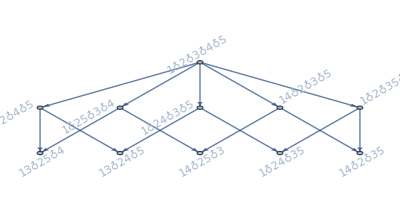

```mathematica
FormulaGraphReverse2[allGraphs5[lambdaKey,"colofour"]]
```

```mathematica
Select[Keys[allGraphs6],IsomorphicGraphQ[allGraphs6[#,"graph"],CycleGraph[6]]&]
```

{6383938,6383890,6379726,6379518,6378274,6378114,5334178,5334130,5316868,5316708,5315464,5315256,4980046,4979838,4966948,4966788,4961172,4961124,4861954,4861794,4848904,4848696,4844532,4844484,2147638,2146186,2134540,2133136,2128764,2128716,1797718,1791894,1780248,1779004,1778796,1774632,1679626,1675254,1662364,1662204,1660752,1656540,734860,730488,729244,729084,715986,711774,616816,612604,612396,610992,599346,593730,262524,262476,258312,256860,245214,243810}

```mathematica
Table[ShowGraph[allGraphs6,k],{k,Select[Keys[allGraphs6],IsomorphicGraphQ[allGraphs6[#,"graph"],CycleGraph[6]]&]}]
```

{-Graphics-6383938,-Graphics-6383890,-Graphics-6379726,-Graphics-6379518,-Graphics-6378274,-Graphics-6378114,-Graphics-5334178,-Graphics-5334130,-Graphics-5316868,-Graphics-5316708,-Graphics-5315464,-Graphics-5315256,-Graphics-4980046,-Graphics-4979838,-Graphics-4966948,-Graphics-4966788,-Graphics-4961172,-Graphics-4961124,-Graphics-4861954,-Graphics-4861794,-Graphics-4848904,-Graphics-4848696,-Graphics-4844532,-Graphics-4844484,-Graphics-2147638,-Graphics-2146186,-Graphics-2134540,-Graphics-2133136,-Graphics-2128764,-Graphics-2128716,-Graphics-1797718,-Graphics-1791894,-Graphics-1780248,-Graphics-1779004,-Graphics-1778796,-Graphics-1774632,-Graphics-1679626,-Graphics-1675254,-Graphics-1662364,-Graphics-1662204,-Graphics-1660752,-Graphics-1656540,-Graphics-734860,-Graphics-730488,-Graphics-729244,-Graphics-729084,-Graphics-715986,-Graphics-711774,-Graphics-616816,-Graphics-612604,-Graphics-612396,-Graphics-610992,-Graphics-599346,-Graphics-593730,-Graphics-262524,-Graphics-262476,-Graphics-258312,-Graphics-256860,-Graphics-245214,-Graphics-243810}

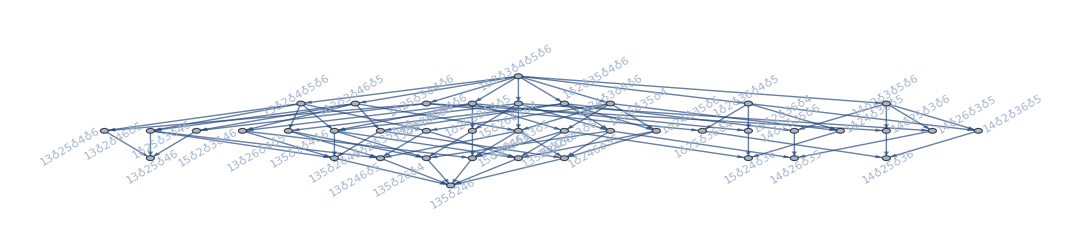

```mathematica
FormulaGraphReverse2[allGraphs6[4861954,"colofour"]]
```